{{y→InterpolatingFunction[…]}}

{{1.,0.},{1.05,0.0453515},{1.1,0.0826446},{1.15,0.113422},{1.2,0.138889},{1.25,0.16},{1.3,0.177515},{1.35,0.192044},{1.4,0.204082},{1.45,0.214031},{1.5,0.222222}}

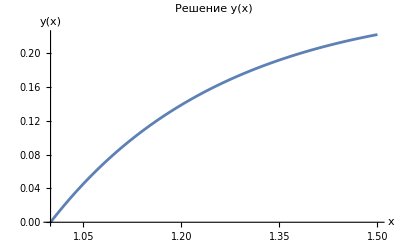

```mathematica
equation=y'[x]==(x^2*y[x]^2-(2x+1)*y[x]+1)/x;
initialCondition=y[1]==0;
solution = NDSolve[{equation,initialCondition}, y, {x, 1, 1.5}]

ySol=y/. First[solution];

points=Range[1.0,1.5,0.05];
values=ySol/@points;

Print[Transpose[{points, values}]]

Plot[Evaluate[y[x]/. solution],{x,1,1.5},PlotLabel->"Решение y(x)",AxesLabel->{"x","y(x)"}]
```